```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
colors=(("DefaultPlotStyle"/.(Method/. Charting`ResolvePlotTheme["Scientific",ListLinePlot]))/. Directive[x_,__]:>x)
markers={"■","●","◆","▲","□","○","◇","△"}
```

{RGBColor[0.9, 0.36, 0.054],RGBColor[0.365248, 0.427802, 0.758297],RGBColor[0.945109, 0.593901, 0.],RGBColor[0.645957, 0.253192, 0.685109],RGBColor[0.285821, 0.56, 0.450773],RGBColor[0.7, 0.336, 0.],RGBColor[0.491486, 0.345109, 0.8],RGBColor[0.71788, 0.568653, 0.],RGBColor[0.70743, 0.224, 0.542415],RGBColor[0.287228, 0.490217, 0.664674],RGBColor[0.982289285128704, 0.5771321368979874, 0.011542503255145636],RGBColor[0.5876740325800278, 0.2877284499870081, 0.7500695697462922],RGBColor[0.4262088601796793, 0.5581552810007578, 0.2777996730417023],RGBColor[0.9431487543762861, 0.414555896337833, 0.07140829055870854],RGBColor[0.41497437140121635, 0.393632147507352, 0.7842993779115092]}

{■,●,◆,▲,□,○,◇,△}

```mathematica
rh=0.1;
rS=0.11;
rp={Sin[θp],
0,
Cos[θp]}*8*10^(-2);
p=10*{0,1,0}*10^(-9) ;
r={x,y,z};
q=Cross[p,rp];
R=r-rp;
f=Simplify[Sqrt[R.R](Sqrt[r.r]Sqrt[R.R]+r.R)];
Bp=Simplify[10^(5)Cross[p,R]/Sqrt[R.R]^3];
B=Simplify[10^(5)*(f q- Dot[q,r]D[f,{{x,y,z}}])/f^2];
```

```mathematica
norm[r_]:=Sqrt[r.r];
n=r/Sqrt[r.r];
er=n;
ez={0,0,1};
eϕ=Cross[ez,er];
eϕ=eϕ/norm@eϕ//Simplify;
eθ=Cross[eϕ,er]//Simplify;
nGeo={Cos@ϕG,0,Sin@ϕG};
```

## Fig1ab

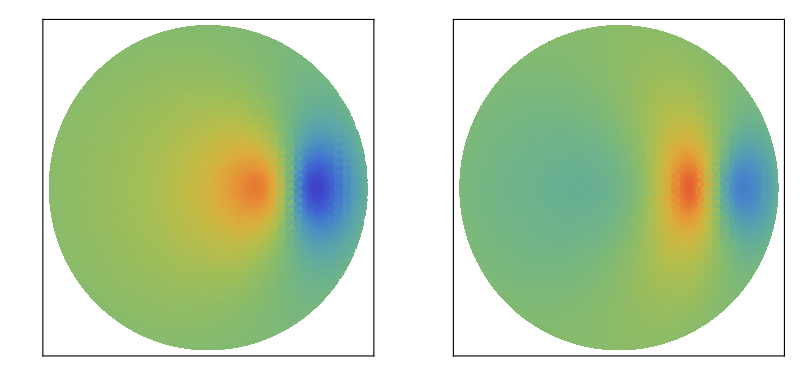

```mathematica
Bs={er.B,B[[1]]}/.{z->Sqrt[rS^2-x^2-y^2],θp->Pi/6}//Simplify;
minVal=-0.5;
maxVal=0.5;
p6ab=DensityPlot[#,{x,y}∈Disk[{0,0},rS],ColorFunctionScaling->False,ColorFunction->Function[f,ColorData["Rainbow"][(f-minVal)/(maxVal-minVal)]],PlotRange->All,FrameLabel->None,FrameTicks->None,PlotPoints->40]&/@Bs;
bar=BarLegend[{"Rainbow",{minVal,maxVal}}];
GraphicsRow[Insert[p6ab,bar,-1],AspectRatio->1/2.5,ImageSize->Full]
```

```mathematica
Do[Export["subplots-final/fig6"<>{"a","b"}[[i]]<>".tiff",p6ab[[i]],ImageResolution->600,ImageSize->1000],{i,2}];
Export["subplots-final/fig6ab-bar.tiff",bar,ImageResolution->600,ImageSize->1000];
```

## fig6cd

```mathematica
g=Exp[-(s-t)^2/w^2];
```

```mathematica
gv=Table[g,{w,{0.1,0.3}},{t,{0.5,0.52}},{s,0,1,1/200}];
```

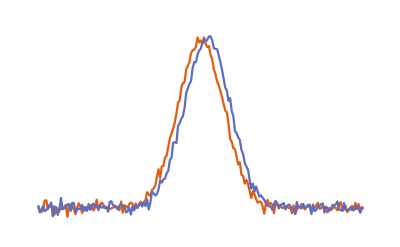
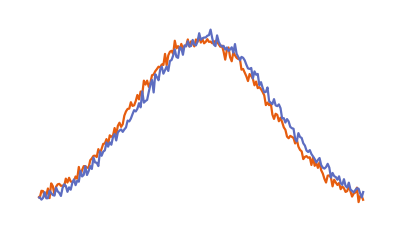

```mathematica
gvn=gv+RandomVariate[NormalDistribution[0,0.02],Dimensions@gv];
p6cd=ListLinePlot[Evaluate@(#),PlotTheme->"Scientific",Frame->False,PlotRange->{-0.1,1.1},PlotStyle->colors,GridLines->None]&/@gvn
```

```mathematica
Do[Export["subplots-final/fig6"<>{"c","d"}[[i]]<>".pdf",p6cd[[i]]],{i,2}];
```

## fig6ef

```mathematica
Bs={er.B,B[[1]]}/.{z->Sqrt[rS^2-x^2],y->0}//Simplify;
```

```mathematica
Bsv=Table[Bs,{θp,Pi/180*{30,33}},{x,-0.11,0.11,0.22/200}];
Bsv=Transpose[Bsv,{2,3,1}];
```

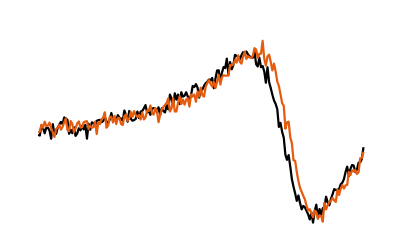
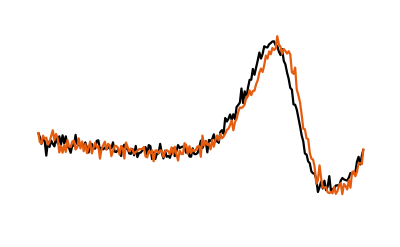

```mathematica
Bsr=Bsv+RandomVariate[NormalDistribution[0,0.02],Dimensions@Bsv];p6ef=ListLinePlot[Evaluate@(#),PlotTheme->"Scientific",Frame->False,PlotRange->{-0.4,0.5},PlotStyle->{Black,colors[[1]]},GridLines->None]&/@Bsr
```

```mathematica
Do[Export["subplots-final/fig6"<>{"e","f"}[[i]]<>".pdf",p6ef[[i]]],{i,2}];
```

```mathematica
Max[Bsv[[1]]]
```

0.362299